(g wb (g uap ub x-ua (g+uap) ubp x-uap ubp (wa+g x)+ua ub (wa+(g+uap) x)))/(2 g^2 (4 wa wb+ua (ub+ubp+2 wb)+uap (ub+ubp+2 wb)) x+wa wb (2 wa wb+uap (2 ubp+wb+wb x))+ua (wa wb (2 ub+wb+wb x)+uap ub (2 ubp+wb+wb x)+uap wb (ubp+ubp x+2 wb x))+g (2 wa wb (ub+ubp+2 (wa+wb x))+uap (ub (2 ubp+wb+wb x)+ubp (2 wa+wb+wb x)+2 wb (wa+wa x+wb x))+ua (ubp (wb+2 uap x+wb x)+ub (2 ubp+2 wa+wb+2 uap x+wb x)+2 wb (wa+2 uap x+wa x+wb x))))

(g uap ub x-ua (g+uap) ubp x-uap ubp (wa+g x)+ua ub (wa+(g+uap) x))/(wa (ua (ub+(2 g+wb) x)-uap (ubp+(2 g+wb) x)))

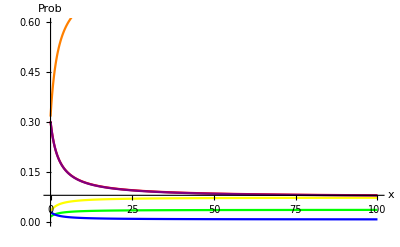

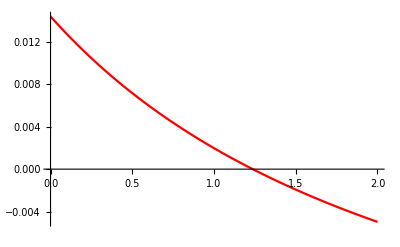

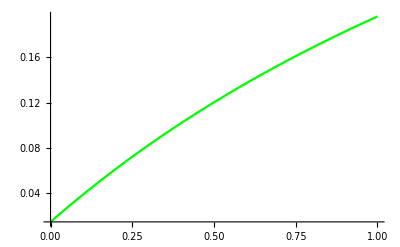

General::openx: PycharmProjects/cotransport/solutiontext.txt is not open.

Close[PycharmProjects/cotransport/solutiontext.txt]

General::openx: PycharmProjects/cotransport/sugar.txt is not open.

Close[PycharmProjects/cotransport/sugar.txt]

OutputStream[…]

OutputStream[…]

PycharmProjects/cotransport/solutiontext.txt

PycharmProjects/cotransport/sugar.txt

{31281861980000/712488629127,True}

```mathematica
Needs["PlotLegends`"]

(*ua = 1000;
uap = 100;
wa = 1000;
wb = 1000;
ub = 900;
ubp = 1000;

g = 100;
x = 0.000000001;

*)
Clear[ua, ub, uap, ubp, wa, wb, g, x]

Clear[x]

(*Clear[p, s, g, x, c, t, q, w, b]*)
mat = {{-(g+ua) ,g ,0,0,0,wa, 0},{g ,-(g+uap),wa,0,0,0, 0},{0,uap,-(g*x+wa+ubp),wb,0,g*x, 0},{0,0,ubp,-(wb + g ),g,0, 0},
{0,0,0,g,-(wb + g),ub, 0},{ua,0,g*x,0,wb,- (g*x + wa + ub), 0}, {1, 1, 1, 1, 1, 1, 1}};
(*mat // MatrixForm
Det[mat]*)
solmat =RowReduce[mat];
(*solmat // MatrixForm*)
pone = solmat[[1, 7]];
ptwo = solmat[[2, 7]];
pthree = solmat[[3, 7]];
pfour = solmat[[4, 7]];
pfive = solmat[[5,7]];
psix = solmat[[6, 7]];



 sugarflowrate = g * pfive - g * pfour;
Simplify[sugarflowrate]

(*g*x*Numerator[pfive] - g/x*Numerator[pfour]*)

aflowrate = g*x*psix - g*x*pthree + g * pfive - g * pfour;
Simplify[Numerator[sugarflowrate]/ Numerator[aflowrate]]


(*Solve[sugarflowrate==0, x]*)
ua = 1000;
uap = 100;
wa = 1000;
wb = 1000;
ub = 100;
ubp = 500;
g = 1;
p1 = Plot[pone, {x, 0, 100}, PlotStyle->Red,  PlotRange -> Full, AxesLabel -> Automatic];
p2 = Plot[ptwo, {x, 0, 100}, PlotStyle->Orange,  PlotRange -> Full, AxesLabel -> Automatic];
p3 = Plot[pthree, {x, 0, 100}, PlotStyle-> Yellow,  PlotRange -> Full, AxesLabel -> Automatic];
p4= Plot[pfour, {x, 0, 100}, PlotStyle-> Green,  PlotRange -> Full, AxesLabel -> Automatic];
p5 = Plot[pfive, {x, 0, 100},PlotStyle -> Blue,  PlotRange -> Full, AxesLabel -> Automatic];
p6 = Plot[psix, {x, 0, 100}, PlotStyle-> Purple,  PlotRange -> Full, AxesLabel -> Automatic];
Show[p1, p2, p3, p4, p5, p6, PlotRange -> {0, .6}, AxesLabel -> {x, "Prob"}]
Plot[sugarflowrate, {x, 0, 2}, PlotStyle->Red, PlotRange->Full]
Plot[aflowrate, {x, 0, 1}, PlotStyle->Green, PlotRange->Full]

Close["PycharmProjects/cotransport/solutiontext.txt"]
Close["PycharmProjects/cotransport/sugar.txt"]
str = OpenWrite["PycharmProjects/cotransport/solutiontext.txt"]
str2 = OpenWrite["PycharmProjects/cotransport/sugar.txt"]
For [x = 0.1, x < 10,x+= 0.1,
thing = ToString[N[{x, {psix, pone, ptwo, pthree, pfour, pfive}}]]; 
Write[str,  thing];
Write[str2, ToString[N[{x, aflowrate, sugarflowrate}]]];]
Close["PycharmProjects/cotransport/solutiontext.txt"]
Close["PycharmProjects/cotransport/sugar.txt"]
(*p2 = Plot[aflowrate, {g, 1, 50000}];
Show[p1, p2, PlotRange -> Full]*)
```